```mathematica
Remove["Global`*"]
```

```mathematica
data= Import["~/Github/math_on_a_comp/RandomNumbers.dat.txt","Table"][[All,1]];
```

```mathematica
Length[data]
Max[data]
Min[data]
Dimensions[data]
N[Mean[data]]
N[Median[data]]
```

250

7.60605

2.26823

{250}

4.89815

4.88669

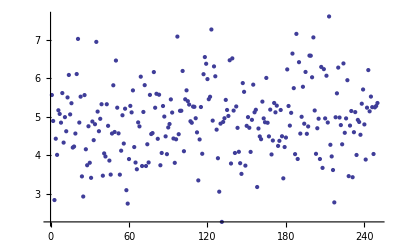

```mathematica
ListPlot[data]
```

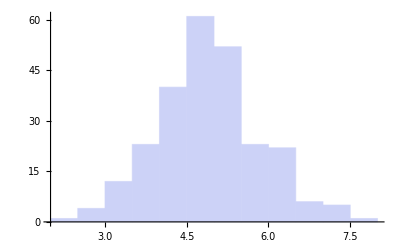

```mathematica
Histogram[data]
```

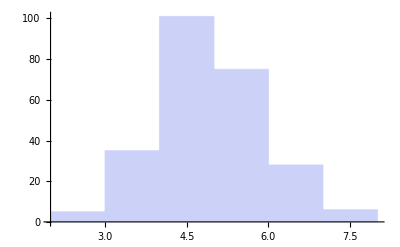

```mathematica
Histogram[data,{{2,3,4,5,6,7,8}}]
```

```mathematica
BinCounts[data]
```

{5,35,101,75,28,6}

```mathematica
BinCounts[data,{{2,3,4,5,6,7,8}}]
```

{5,35,101,75,28,6}

```mathematica
BinCounts[Flatten[data],{0,10,.5}]
```

{0,0,0,0,1,4,12,23,40,61,52,23,22,6,5,1,0,0,0,0}

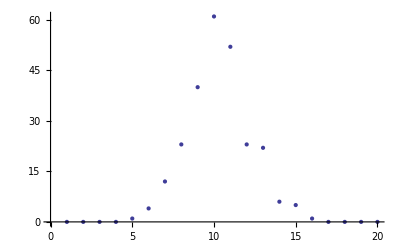

```mathematica
ListPlot[BinCounts[Flatten[data],{0,10,.5}]]
```

```mathematica
model = a*Exp[-(b+x)^2/(2*c^2)]
```

a ⅇ^(-(b+x)^2/(2 c^2))

```mathematica
fitParams = FindFit[BinCounts[Flatten[data],{0,10,.5}],{model},{a,b,c},x]
```

{a→56.2848,b→-10.2035,c→1.70589}

```mathematica
modelFit = Function[{x},Evaluate[model/.fitParams]]
```

Function[{x},56.2848 ⅇ^(-0.171817 (-10.2035+x)^2)]

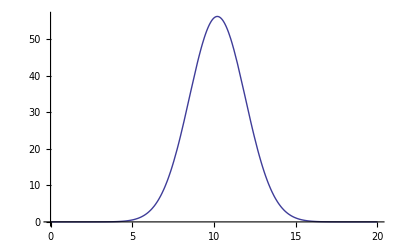

```mathematica
Plot[modelFit[x],{x,0,20}]
```

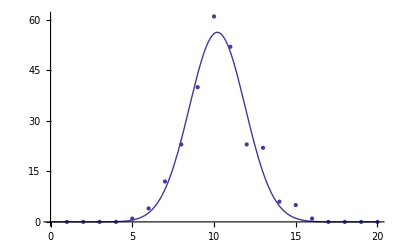

```mathematica
Show[ListPlot[BinCounts[Flatten[data],{0,10,.5}]], Plot[modelFit[x],{x,0,20}]]
```

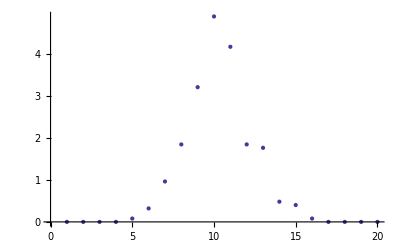

```mathematica
dataToFit = BinCounts[Flatten[data],{0,10,.5}]/N[Mean[BinCounts[Flatten[data],{0,10,.5}]]];
ListPlot[dataToFit]
```

(ⅇ^(-(b+x)^2/(2 c^2)))/(√(c^2) √(2 π))

{b→-10.0073,c→0.081419}

Function[{x},4.89987 ⅇ^(-75.4255 (-10.0073+x)^2)]

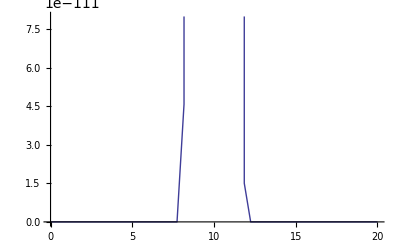

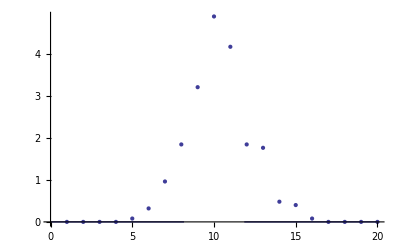

```mathematica
model = (1/√(2*Pi*c^2))*Exp[-(b+x)^2/(2*c^2)]
fitParams = FindFit[dataToFit,{model},{b,c},x]
modelFit = Function[{x},Evaluate[model/.fitParams]]
Plot[modelFit[x],{x,0,20}]
Show[ListPlot[dataToFit], Plot[modelFit[x],{x,0,20}]]
```

```mathematica
Range[Length[data]];
```

```mathematica
Remove["Global`*"]
dataToFit = {{0,0},{Pi/4,1/√2},{Pi/6,1/2},{Pi/2,1},{Pi/3,√3/2},{2Pi/3,√3/2},{5Pi/6,1/2},{Pi,0}}
```

{{0,0},{π/4,1/(√2)},{π/6,1/2},{π/2,1},{π/3,(√3)/2},{(2 π)/3,(√3)/2},{(5 π)/6,1/2},{π,0}}

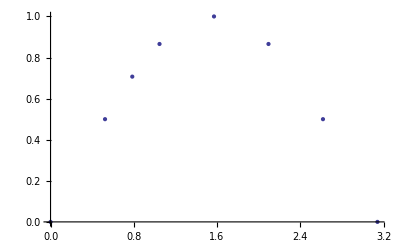

```mathematica
ListPlot[dataToFit]
```

```mathematica
sfl = Fit[dataToFit,{1,x,x^2},x]
```

-0.0170307+1.25262 x-0.398264 x^2

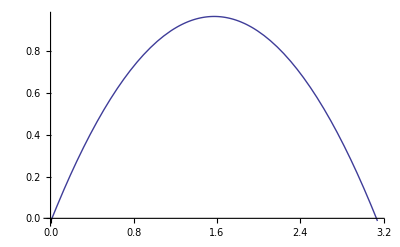

```mathematica
Plot[sfl,{x,0,Pi}]
```

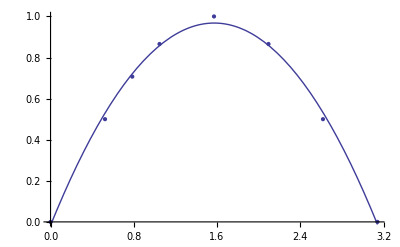

```mathematica
Show[ListPlot[dataToFit],Plot[sfl,{x,0,Pi}]]
```

```mathematica
Fit[dataToFit,{1,Sin[x]},x]
```

1.57009×10^-16+1. Sin[x]

```mathematica
Remove["Global`*"]
```

```mathematica
dataToFit = Table[{x,Exp[x]},{x,0,5}]
```

{{0,1},{1,ⅇ},{2,ⅇ^2},{3,ⅇ^3},{4,ⅇ^4},{5,ⅇ^5}}

```mathematica
testFit = Fit[dataToFit,{1,x,x^2,x^3},x]
```

-0.0981699+15.0847 x-12.0845 x^2+2.99186 x^3

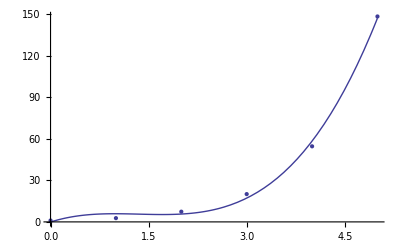

```mathematica
Show[ListPlot[dataToFit],Plot[testFit,{x,0,5}]]
```

```mathematica
testFit = Fit[dataToFit,{1,Cosh[x]},x]
```

-0.395901+2.00676 Cosh[x]

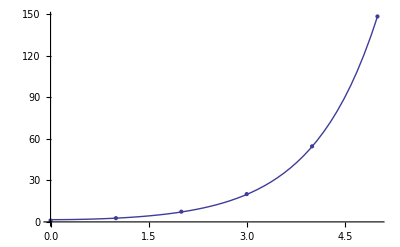

```mathematica
Show[ListPlot[dataToFit],Plot[testFit,{x,0,5}]]
```

```mathematica
testFit = Fit[dataToFit,{1,Cosh[x],Sinh[x]},x]
```

-2.56187×10^-15+1. Cosh[x]+1. Sinh[x]

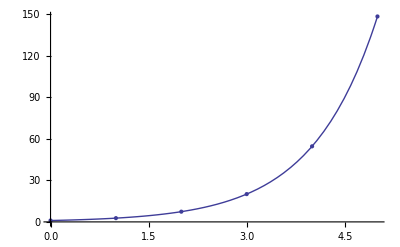

```mathematica
Show[ListPlot[dataToFit],Plot[testFit,{x,0,5}]]
```

```mathematica
dataToFit
```

{{0,1},{1,ⅇ},{2,ⅇ^2},{3,ⅇ^3},{4,ⅇ^4},{5,ⅇ^5}}

```mathematica
dataToFit[[1]]
```

{0,1}

```mathematica
Needs["LinearRegression`"]
```

General::obspkg: "LinearRegression`" is now obsolete. The legacy version being loaded may conflict with current Mathematica functionality. See the Compatibility Guide for updating information.

```mathematica
Regress[dataToFit,{1,Cosh[x],Sinh[x]},x,RegressionReport->RSquared]
```

{RSquared→1.}

```mathematica
Regress[dataToFit,{1,Cosh[x],Sinh[x^2]},x,RegressionReport->RSquared]
```

{RSquared→0.999974}

```mathematica
Regress[dataToFit,{1,x, x^2},x,RegressionReport->RSquared]
```

{RSquared→0.962132}

```mathematica
Remove["Global`*"]
```

```mathematica
dataToFit = Import["~/Github/math_on_a_comp/Cs137.dat.txt","Table"]
```

{{0,283},{1,249},{2,209},{3,239},{4,216},{5,203},{6,185},{7,165},{8,148},{9,127},{10,123},{11,131},{12,99},{13,98},{14,90},{15,90},{16,88},{17,59},{18,55},{19,52},{20,56},{21,76},{22,46},{23,43},{24,43},{25,36},{26,43},{27,37},{28,33},{29,37},{30,24},{31,42},{32,27},{33,34},{34,25},{35,22},{36,29},{37,23},{39,10},{40,17},{41,12},{42,19},{43,16},{44,13},{45,16},{46,13},{47,18},{48,7},{49,12},{50,19},{51,18},{52,12},{53,15},{54,11},{55,8},{56,12},{57,9},{58,14},{59,16},{60,12},{61,12},{62,8},{63,9},{64,10},{65,14},{66,10},{67,10},{68,14},{69,6},{70,11},{71,13},{72,14},{73,11},{74,12},{75,8},{76,12},{77,15},{78,6},{79,15},{80,10},{81,10},{82,10},{83,10},{84,12},{85,4},{86,7},{87,9},{88,9},{89,15},{90,9},{91,13},{92,7},{93,12},{94,7},{95,13},{96,11},{97,14},{98,14},{99,11},{100,11}}

```mathematica
Length[dataToFit]
Max[dataToFit]
Min[dataToFit]
Dimensions[dataToFit]
N[Mean[dataToFit]]
N[Median[dataToFit]]
```

100

283

0

{100,2}

{50.12,43.12}

{50.5,14.5}

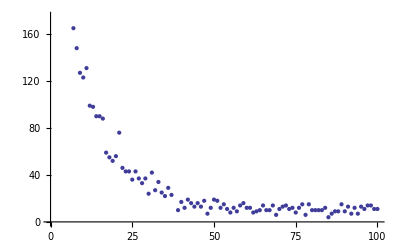

```mathematica
ListPlot[dataToFit]
```

```mathematica
model = a*Exp[-b*t]
```

a ⅇ^(-b t)

```mathematica
fitParams = FindFit[dataToFit,{model},{a,b},t]
```

{a→272.771,b→0.0736178}

Function[{t},272.771 ⅇ^(-0.0736178 t)]

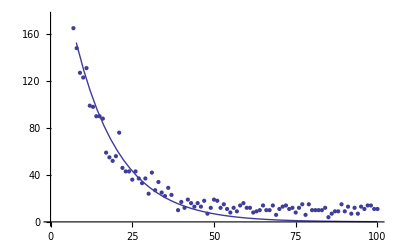

```mathematica
modelFit = Function[{t},Evaluate[model/.fitParams]]
Show[ListPlot[dataToFit], Plot[modelFit[t],{t,0,100}]]
```

```mathematica
dataFit =Table[modelFit[t],{t,1,100}]
```

{253.412,235.426,218.717,203.194,188.773,175.375,162.928,151.365,140.622,130.641,121.369,112.755,104.753,97.318,90.411,83.9943,78.0329,72.4947,67.3495,62.5695,58.1287,54.0031,50.1703,46.6096,43.3016,40.2283,37.3732,34.7207,32.2564,29.9671,27.8402,25.8643,24.0286,22.3232,20.7389,19.267,17.8995,16.6292,15.4489,14.3525,13.3338,12.3875,11.5083,10.6915,9.9327,9.22775,8.57282,7.96438,7.39912,6.87398,6.38611,5.93287,5.5118,5.1206,4.75718,4.41955,4.10588,3.81447,3.54374,3.29223,3.05857,2.84149,2.63982,2.45247,2.27841,2.1167,1.96647,1.82691,1.69724,1.57679,1.46488,1.36091,1.26432,1.17459,1.09122,1.01378,0.941824,0.87498,0.81288,0.755187,0.701589,0.651795,0.605535,0.562558,0.522631,0.485539,0.451078,0.419064,0.389321,0.36169,0.33602,0.312171,0.290015,0.269432,0.25031,0.232544,0.21604,0.200707,0.186462,0.173228}

```mathematica
diff = dataToFit[[All,2]] - dataFit
```

{29.5883,13.5738,-9.71725,35.8058,27.2272,27.625,22.072,13.6355,7.37833,-3.64129,1.63076,18.2447,-5.75266,0.681984,-0.411036,6.00573,9.96708,-13.4947,-12.3495,-10.5695,-2.12871,21.9969,-4.17034,-3.60959,-0.301551,-4.2283,5.62684,2.27933,0.743573,7.03292,-3.84022,16.1357,2.97137,11.6768,4.26111,2.73302,11.1005,6.37085,-5.44892,2.64754,-1.33382,6.61252,4.4917,2.30848,6.0673,3.77225,9.42718,-0.964382,4.60088,12.126,11.6139,6.06713,9.4882,5.8794,3.24282,7.58045,4.89412,10.1855,12.4563,8.70777,8.94143,5.15851,6.36018,7.54753,11.7216,7.8833,8.03353,12.1731,4.30276,9.42321,11.5351,12.6391,9.73568,10.8254,6.90878,10.9862,14.0582,5.12502,14.1871,9.24481,9.29841,9.34821,9.39447,11.4374,3.47737,6.51446,8.54892,8.58094,14.6107,8.63831,12.664,6.68783,11.71,6.73057,12.7497,10.7675,13.784,13.7993,10.8135,10.8268}

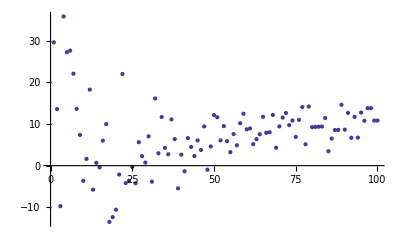

```mathematica
ListPlot[diff]
```

```mathematica
N[1/0.07361778851033923]
```

13.5837

a-b t

{a→4.68167,b→0.0310258}

Function[{t},4.68167-0.0310258 t]

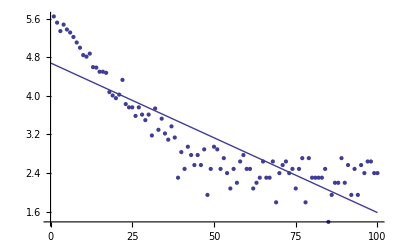

```mathematica
model = a - b*t
fitParams = FindFit[N[Log[dataToFit[[All,2]]]],{model},{a,b},t]
modelFit = Function[{t},Evaluate[model/.fitParams]]
Show[ListPlot[Log[dataToFit[[All,2]]]], Plot[modelFit[t],{t,0,100}]]
```

```mathematica
diffLogFit =Log[dataToFit[[All,2]]] -Table[modelFit[t],{t,1,100}]
```

{0.994807,0.897839,0.753746,0.918901,0.848742,0.817695,0.755871,0.672487,0.594779,0.47278,0.471803,0.565842,0.31679,0.337664,0.283532,0.314557,0.32311,-0.0456632,-0.0848416,-0.109905,-0.0047715,0.331636,-0.13943,-0.175846,-0.14482,-0.291475,-0.0827682,-0.202025,-0.285409,-0.139973,-0.541811,0.0488304,-0.361977,-0.100427,-0.376886,-0.473693,-0.166414,-0.36719,-1.16907,-0.607419,-0.9247,-0.434142,-0.574966,-0.75158,-0.512915,-0.689528,-0.33308,-1.24652,-0.676494,-0.185935,-0.208977,-0.583416,-0.329247,-0.608376,-0.895804,-0.459313,-0.715969,-0.243111,-0.0785533,-0.33521,-0.304184,-0.678623,-0.529814,-0.393428,-0.0259298,-0.331376,-0.30035,0.0671476,-0.749124,-0.111963,0.0861171,0.191251,-0.0188853,0.0991519,-0.275287,0.161204,0.415373,-0.469892,0.477425,0.102985,0.134011,0.165037,0.196063,0.40941,-0.658176,-0.0675348,0.214805,0.245831,0.787683,0.307883,0.706633,0.11862,0.688642,0.180672,0.830737,0.694709,0.966896,0.997922,0.787786,0.818812}

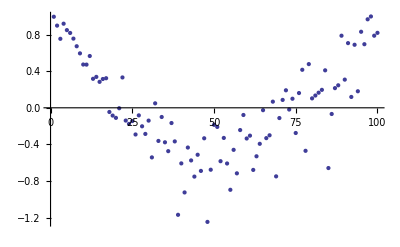

```mathematica
ListPlot[diffLogFit]
```

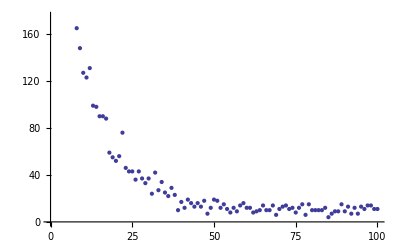

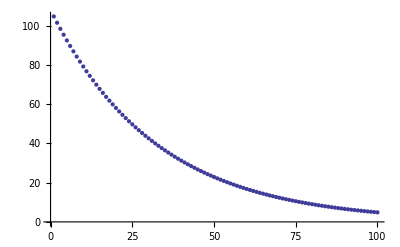

```mathematica
Show[ListPlot[dataToFit[[All,2]]]]
ListPlot[Exp[Table[modelFit[t],{t,1,100}]]]
```

{178.348,147.545,110.645,143.649,123.562,113.386,98.1238,80.7778,66.3507,47.8451,46.2632,56.6075,26.8801,28.0833,22.2193,24.2899,24.2973,-2.75659,-4.86996,-6.04096,-0.267843,21.4511,-6.88245,-8.26692,-6.70074,-12.1824,-3.71047,-8.28349,-10.9001,-5.55898,-17.2588,2.00161,-11.7765,-3.59186,-11.4434,-13.3301,-5.25081,-10.2045,-22.1901,-14.2067,-18.2533,-10.3291,-12.4331,-14.5645,-10.7224,-12.9061,-7.11466,-17.3474,-11.6036,-3.88255,-4.1835,-9.5058,-5.84881,-9.21189,-11.5944,-6.99583,-9.41552,-3.85293,-1.30754,-4.7788,-4.26622,-7.76929,-6.28755,-4.82052,-0.367765,-3.92884,-3.50332,0.9092,-6.69088,-1.30318,1.07267,2.43705,-0.209713,1.13274,-2.53527,1.78657,5.09859,-3.59893,5.69431,0.978597,1.2542,1.52138,1.78039,4.0315,-3.72507,-0.489072,1.73971,1.96151,8.17653,2.38499,6.58707,0.782984,5.97291,1.15703,7.33553,5.50858,8.67634,8.83898,5.99664,6.14949}

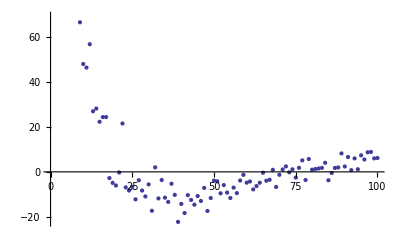

```mathematica
diffFit = dataToFit[[All,2]] -Exp[Table[modelFit[t],{t,1,100}]]
ListPlot[diffFit]
```

```mathematica
N[1/0.031025819073912657]
```

32.2312